```mathematica
m=Table[{n,1-n,((n^2*.09)+((1-n)^2*0.0225)+(2*n*(1-n)*0.0045))^0.5,(n*.2)+(.12*(1-n))},{n,0,1,0.2}];
TableOfValues1=Prepend[m,{"Percent in Stocks","Percent in Bonds","Standard Deviation","Expected Return"}];
Grid[TableOfValues1, Frame->All]
```

Percent in Stocks | Percent in Bonds | Standard Deviation | Expected Return
0. | 1. | 0.15 | 0.12
0.2 | 0.8 | 0.139427 | 0.136
0.4 | 0.6 | 0.157035 | 0.152
0.6 | 0.4 | 0.195346 | 0.168
0.8 | 0.2 | 0.244826 | 0.184
1. | 0. | 0.3 | 0.2

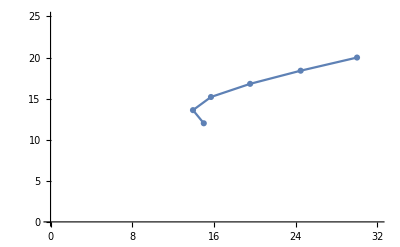

```mathematica
x=Table[{((n^2*.09)+((1-n)^2*0.0225)+(2*n*(1-n)*0.0045))^0.5,(n*.2)+(.12*(1-n))},{n,0,1,0.2}];
ListPlot[x*100,PlotRange->{{0,32},{0,25}}, Joined->True,PlotMarkers->Automatic]
```